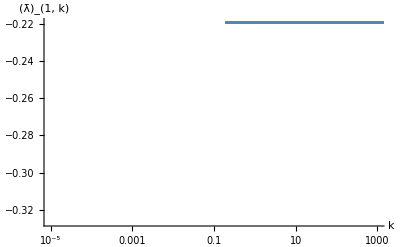

```mathematica
SetDirectory[NotebookDirectory[]];
k=Flatten[Import["./k1.dat"]];
lam1=Flatten[Import["./lam1.dat"]]*197.33^2;
lam2=Flatten[Import["./lam2.dat"]];
lam3=Flatten[Import["./lam3.dat"]]/197.33^2;
lam1dl=lam1[[1;;Length[k]]]*k^-2;
lam2dl=lam2[[1;;Length[k]]]*131.470493375/k;
lam3dl=lam3[[1;;Length[k]]]*131.470493375^2;
plotl1=ListLinePlot[Transpose[{k*197.33,lam1dl}],PlotRange->{{10^-5,1000},All},ScalingFunctions->{"Log",Automatic},AxesLabel->{"k","(λ̄)_(1, k)"}]
```

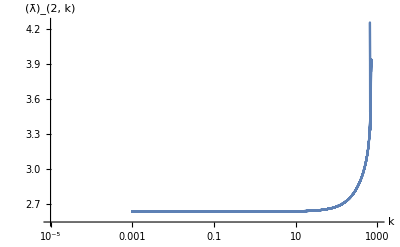

```mathematica
plotl2=ListLinePlot[Transpose[{k,lam2dl}],PlotRange->{{10^-5,1000},All},ScalingFunctions->{"Log",Automatic},AxesLabel->{"k","(λ̄)_(2, k)"}]
```

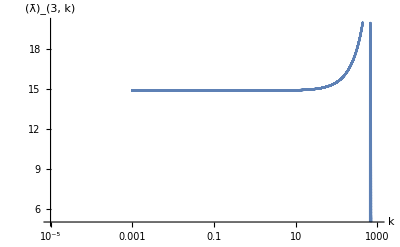

```mathematica
plotl3=ListLinePlot[Transpose[{k,lam3dl}],PlotRange->{{10^-5,1000},{5,20}},ScalingFunctions->{"Log",Automatic},AxesLabel->{"k","(λ̄)_(3, k)"}]
```

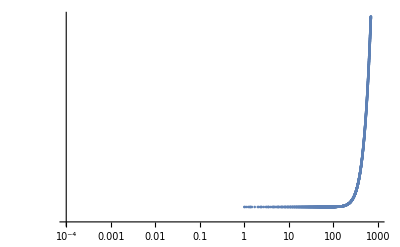

```mathematica
ListPlot[Transpose[{k*197.33,lam2}],PlotRange->{{10^-4,1000},All},ScalingFunctions->{"Log","Log"}]
```

```mathematica
T=Flatten[Import["./TMeV.dat"]];
sigma=Flatten[Import["./fpi.dat"]];
mp=Flatten[Import["./mPion.dat"]];
```

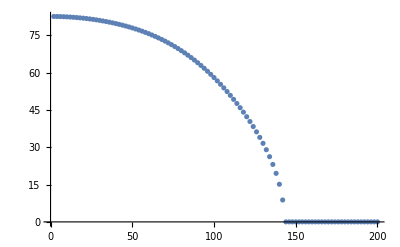

```mathematica
ListPlot[Transpose[{T,sigma}]]
```

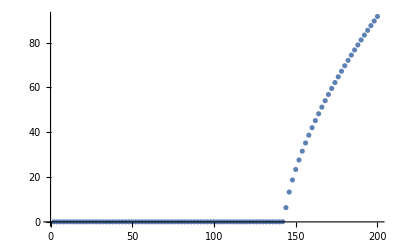

```mathematica
ListPlot[Transpose[{T,mp}]]
```

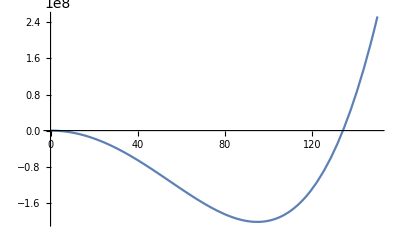

```mathematica
Plot[((sigma^2/2)^2*20)/2-300^2(sigma^2/2),{sigma,0,150}]
```